# What is the distribution of the sum of K_n random variables?

One way to attack the issue of time-averaged class richness is to ask what happens when we add a number of RV’s which represent the distribution of trait counts in a sample.  Ewens (2004) gives the full distribution of K_n, the random variable describing the number of alleles in a sample of size n, as Equation 3.84.

```mathematica
Clear[n, x,  f, k, θ]
```

```mathematica
f = (Abs[StirlingS1[n,x]] θ^x) / Pochhammer[θ, n] ; 
domain[f] = {x , 1, n}  && {n ∈Integers} && {θ > 0, n > 0} && {Discrete};
```

```mathematica
Expect[x, f]
```

∑_(x=1)^n (x θ^x Abs[StirlingS1[n,x]])/Pochhammer[θ,n]

## Does this function work properly?

Need to test whether this formula actually works, despite looking correct as a Mathematica translation of Ewens’s (1972) equation.  So I looked at data in Ewens 2004, Section 9.5.2, in which the mean number of alleles (K_n) is tabulated for n = 200, with different theta values, from the time-dependent frequency spectrum.  Using the “infinity” time column, representing stationarity, the value for θ = 1.0 should be 5.88 alleles.  Similarly, the value for θ = 1.5 should be 7.90 alleles.  

The accuracy looks extremely good here, and thus the PMF listed above is an accurate distribution for K_n.

```mathematica
On[General::stop]
```

```mathematica
Clear[n, x, k, θ]
```

```mathematica
Expect[x, f /. {θ -> 1.0, n -> 200}]// N
```

5.87803

```mathematica
Expect[x, f/. {θ -> 1.5, n -> 200}] // N
```

7.90022

```mathematica
Expect[x, f /. {θ -> 5.0, n -> 30}] // N
```

10.1744

```mathematica
Expect[x, f /. {θ -> 10.0, n -> 30}] // N
```

14.2457

```mathematica
Expect[x, f /. {θ -> 11.2724, n -> 30}] // N
```

15.

```mathematica
Var[x, f /.  {θ -> 1.5, n -> 200}] // N
```

5.80811

```mathematica
RandomNumber[20, f /. {θ -> 1.5, n -> 200}]
```

{8,11,5,8,6,9,8,14,3,9,13,8,5,13,7,10,4,8,10,7}

domain::numeric: This function can only work if ALL parameters have been assigned numerical values. Please check that f meets this requirement.

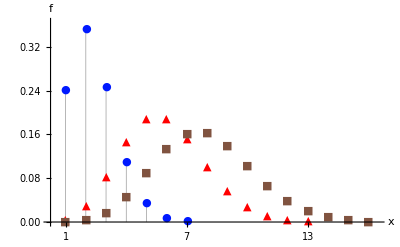

```mathematica
PlotDensity[f /. {θ -> {1/4, 1, 3/2}, n -> 200}]
```

## Sum of K_n Distributed Random Variables -- First Cut at Time-Averaging

A first try at determining the distribution of the expected number of variants in a time-averaged sample could be given simply by the sum of a series of variables distributed as above.  This may be an overestimate of K_n-ta, because it would not account for those variants which are shared across time-slices being accumulated.  A good estimate would thus require a correction for the expected overlap between time-slices.  

We should not expect an exact symbolic answer to this question, because Mathematica cannot do anything further with the distribution of K_n, but we should be able to do a proper sum of K_n random variables and examine their empirical density, create random samples from the summed distribution, and estimate variance.  Which would be enough to start looking at empirical cases.  

First I take the moment-generating function approach to summing the random variables, since it leads easily to an estimate of variance as well as the mean of the sample sum.

```mathematica
mgfs1 = Expect[ⅇ^{tx}, f, Assumptions -> t ∈Reals]^d
```

{(∑_(x=1)^n (ⅇ^tx θ^x Abs[StirlingS1[n,x]])/Pochhammer[θ,n])^d}

### Transformation Approach

```mathematica
fjoint = ((Abs[StirlingS1[n,x1]] θ1^x1) / Pochhammer[θ1, n] )((Abs[StirlingS1[n,x2]] θ2^x2) / Pochhammer[θ2, n] ); 
domain[fjoint] = {{x1 , 1, n},{x2, 1, n}}  && {n ∈Integers} && {θ 1> 0, θ2 > 0, n > 0} && {Discrete};
```

```mathematica
fjoint
```

(θ1^x1 θ2^x2 Abs[StirlingS1[n,x1]] Abs[StirlingS1[n,x2]])/(Pochhammer[θ1,n] Pochhammer[θ2,n])

```mathematica
g = Transform[{y == x1 + x2, z == x2}, fjoint]
```

(θ1^(y-z) θ2^z Abs[StirlingS1[n,y-z]] Abs[StirlingS1[n,z]])/(Pochhammer[θ1,n] Pochhammer[θ2,n])

```mathematica
sol = Sum[g,{z,0,y}]
```

∑_(z=0)^y (θ1^(y-z) θ2^z Abs[StirlingS1[n,y-z]] Abs[StirlingS1[n,z]])/(Pochhammer[θ1,n] Pochhammer[θ2,n])

```mathematica
domain[sol] = {{y, 1, n}, {z, 1, n}}
```

{{y,1,n},{z,1,n}}

```mathematica
Expect[y, sol /. {θ1 -> 1.5, θ2 -> 1.5, n->200}] // N
```

NSum::nslim: Limit of summation y is not a number.

General::stop: Further output of NSum :: nslim will be suppressed during this calculation.

3.9799×10^6 NSum[6.29008784345252×10^-753 1.5^y Abs[StirlingS1[200,y-z]] Abs[StirlingS1[200,z]],{z,0,y}]

Problem - clearly I’m doing something wrong here.  Or perhaps it cannot really work with transformations on PMFs that it cannot solve.

## Normal Approximation to the PMF of K_n

Watterson describes approximations to the full distribution of K_n, and that the distribution is Poisson-Normal at large samples. In this section, I employ Watterson’s approximations and compare to the expected values from the exact distribution given in Ewens 3.84.  This could be particularly useful in calculating sums of these random variables.

```mathematica
μ = 1/2 θ [2 log N + 1.355076]
```

1/2 θ[1.35508+2 log N]

```mathematica
σ = √(μ + (θ^2)( π^2/6))
```

√((π^2 θ^2)/6+1/2 θ[1.35508+2 log N])

Normal		Variable:   -∞<x<∞		Parameters:  μ∈ℝ (location, mean),    σ>0 (scale, standard deviation)

```mathematica
h= 1/(σ √(2 π))Exp[-(x-μ)^2/(2 σ^2)];      domain[h] = {x,-∞,∞} && {μ∈Reals,σ>0};
```

```mathematica
h
```

(ⅇ^(-(x-1/2 θ[1.35508+2 log N])^2/(2 ((π^2 θ^2)/6+1/2 θ[1.35508+2 log N]))))/(√(2 π) √((π^2 θ^2)/6+1/2 θ[1.35508+2 log N]))

Now we have a distribution which approximates K_n but without mention of the actual sample size, and instead requires the population size.  Not great, but useful for figuring out how closely the Watterson approximation matches the exact values calculated above.  

Using the θ value of 1.5 from the above examples, if we assume mutation rate μ = 0.0001, this gives total N of 3750 in the population.  Let’s compare the exact and approximate distributions.  The exact version, with a sample of 200 genes, gives 7.90 variants expected.

```mathematica
h
```

(ⅇ^(-(x-1/2 θ[1.35508+2 log N])^2/(2 ((π^2 θ^2)/6+1/2 θ[1.35508+2 log N]))))/(√(2 π) √((π^2 θ^2)/6+1/2 θ[1.35508+2 log N]))

```mathematica
Expect[x, h /. {θ->1.5, N -> 3750}] // N
```

NIntegrate::inumr: The integrand ⅇ^-0.125\ (« 1 » - « 1 »)^2/3.7011  + 0.5\ « 1 »\ x/√23.2547  + 3.14159\ 1.5[1.35508  + 7500.\ log]
 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-∞, 0.}}.

NIntegrate[(ⅇ^(-(0.125 (2. x-1. 1.5[1.35508+7500. log])^2)/(3.7011+0.5 1.5[1.35508+7500. log])) x)/(√(23.2547+3.14159 1.5[1.35508+7500. log])),{x,-∞,∞}]

```mathematica
m = FullSimplify[μ /.  {θ->1.5, N -> 3750} ]
```

1/2 1.5[1.35508+7500. log]

```mathematica
m = N[%30]
```

NIntegrate[(2.71828^(-(0.125 (2. x-1. 1.5[1.35508+7500. log])^2)/(3.7011+0.5 1.5[1.35508+7500. log])) x)/(√(23.2547+3.14159 1.5[1.35508+7500. log])),{x,-∞,∞}]

```mathematica
mean = 1/2 θ [2 log popsize + 1.355076]
```

1/2 θ[1.35508+2 log popsize]

```mathematica
example = mean /. {θ->1.5, popsize -> 3750}
```

1/2 1.5[1.35508+7500 log]

```mathematica
N[mean /. {θ->1.5, popsize -> 3750}]
```

0.5 1.5[1.35508+7500. log]

```mathematica
N[mean] /. {θ->1.5, popsize -> 3750}
```

0.5 1.5[1.35508+7500. log]

```mathematica
mean
```

1/2 θ[1.35508+2 log popsize]

```mathematica
stdev = √(mean + (θ^2)( π^2/6))
```

√((π^2 θ^2)/6+1/2 θ[1.35508+2 log popsize])

```mathematica
dist = NormalDistribution[mean, stdev] /. {θ->1.5, popsize -> 3750}
```

NormalDistribution[1/2 1.5[1.35508+7500 log],√(3.7011+1/2 1.5[1.35508+7500 log])]

```mathematica
Expect[x, NormalDistribution[mean, stdev] /. {θ->1.5, popsize -> 3750}] // N
```

domain::s: You need to specify the domain for density NormalDistribution[mean, stdev]. For example: 
       domain[NormalDistribution[mean, stdev]] = {x, 0, 1} 
 Please do this. Then try again.